```mathematica
array1 = Import["C:\Users\Mr\Workspace\MPLAB_projects\dspic33_FFT_DSPLib.X\adc_samples.mch","Text"];
```

```mathematica
array2=StringSplit[array1]
```

{0821,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001,0000,0000,0000,0001,0000,0001,0001,00BD,0002,0000,0000,0000,0000,0000,0000,0002,0001,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0002,003E,0005,0001,0000,0001,0000,0001,0003,0018,0027,0005,0001,0001,0001,0000,0000,0000,0001,0001,0001,0001,000B,0032,0001,0000,0000,0000,0000,0000,0000,0001,0000,0000,0000,0000,0000,0000,0000,0002,0000,0000,0000,0004,0004,0001,0000,0000,0000,0000,0000,0000,0001,0000,0000,0000,0000,0000,0001,0002,003D,0004,0001,0000,0000,0002,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0002,0001,0000,0000,0000,0003,0005,0001,0001,0000,0000,0000,0000,0001,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001,0001,0000,0000,0002,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0005,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001,0001,0001,0000,0000,0001,0000,0000,0000,0000,0001,0002,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001,0001,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0000,0001}

```mathematica
array3=FromDigits[#,16]&/@ array2
```

{2081,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,189,2,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,2,62,5,1,0,1,0,1,3,24,39,5,1,1,1,0,0,0,1,1,1,1,11,50,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,4,4,1,0,0,0,0,0,0,1,0,0,0,0,0,1,2,61,4,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,3,5,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

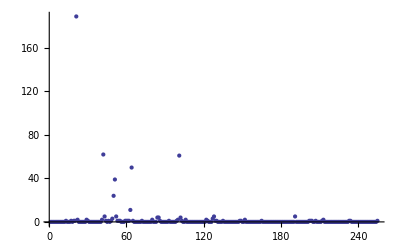

```mathematica
ListPlot[array3[[2;;]],ImageSize->Full,PlotRange->Full]
```